```mathematica
Vlj[R_,σ_] = 4*(  (σ/ R)^12 -  (σ/R)^6 )
```

4 (-σ^6/R^6+σ^12/R^12)

```mathematica
Vsmooth[b_,R_,rc_] =  b* (R-rc)^2
```

b (R-rc)^2

```mathematica
Clear[σ]
Clear[R]
mysigma = 0.5
myrstar = 0.5+0.15 
D[Vlj[R,σ],R] 


Solve[{Vlj[R,σ] == Vsmooth[b,R,rc],
D[Vlj[R,σ],R] == D[Vsmooth[b,R,rc],R]},{b,rc}]
```

0.5

0.65

4 ((6 σ^6)/R^7-(12 σ^12)/R^13)

{{b→(36 σ^6 (-R^6+2 σ^6)^2)/(R^14 (-R^6+σ^6)),rc→(R (4 R^6-7 σ^6))/(3 (R^6-2 σ^6))}}

```mathematica
EXCVol[R_,b_,σ_,rc_,rstar_] = Piecewise[{ {Vlj[R,σ],R<rstar}, {Vsmooth[b,R,rc],rstar<R < rc},{0,R>rc}}]
```

```mathematica
Piecewise[{{4 (-σ^6/R^6+σ^12/R^12), R<rstar}, {b (R-rc)^2, rstar<R<rc}, {0, True}}]
```

```mathematica
sol = {{b->(36 σ^6 (-R^6+2 σ^6)^2)/(R^14 (-R^6+σ^6)),rc->(R (4 R^6-7 σ^6))/(3 (R^6-2 σ^6))}} /. {σ->1.5,R->1.45}
```

{{b→195.903,rc→1.52513}}

```mathematica
{{b->13401.661254320163,rc->0.456610444133461}}
```

{{b→13401.7,rc→0.45661}}

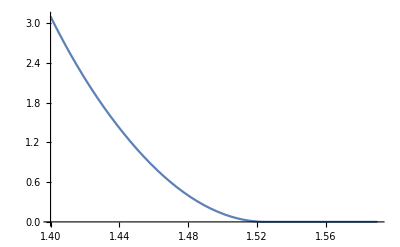

```mathematica
Plot[EXCVol[x,b,1.5,rc,1.45] /. sol,{x,1.40,1.59}]
```